```mathematica
(*When using bash;
  Variables v.s. nAtom*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Parameters*)
nMax=38;
init=10;
interval=10;
repumping = 10;
(*Get data*)
(*Set up bins*)
intensity=Table[0,{i,nMax}];
intensityUnCor=Table[0,{i,nMax}];
inversion =Table[0,{i,nMax}];
spinSpinCor=Table[0,{i,nMax}];
nAtom=Table[0,{i,nMax}];
(*Input values*)
For[i=0,i<nMax,i++,
nAtom[[i+1]] = init+interval i;
intensityData=Flatten[Import[NotebookDirectory[]<>"N"<>ToString[nAtom[[i+1]]]<>"_repumping"<>ToString[repumping]<>"/intensity.dat"]];
intensityUnCorData=Flatten[Import[NotebookDirectory[]<>"N"<>ToString[nAtom[[i+1]]]<>"_repumping"<>ToString[repumping]<>"/intensityUnCor.dat"]];
inversionData=Flatten[Import[NotebookDirectory[]<>"N"<>ToString[nAtom[[i+1]]]<>"_repumping"<>ToString[repumping]<>"/inversion.dat"]];
spinSpinCorData=Flatten[Import[NotebookDirectory[]<>"N"<>ToString[nAtom[[i+1]]]<>"_repumping"<>ToString[repumping]<>"/spinSpinCor.dat"]];
(*x=Cases[x,Except[0|0.]];*)
intensity[[i+1]]=Last[intensityData];
intensityUnCor[[i+1]]=Last[intensityUnCorData];
inversion[[i+1]]=Last[inversionData];
spinSpinCor[[i+1]]=Last[spinSpinCorData];
]
```

```mathematica
(*Combine data*)
intensityPlot=Transpose@{ nAtom,intensity};
intensityUnCorPlot=Transpose@{ nAtom,intensityUnCor};
inversionPlot=Transpose@{nAtom,inversion};spinSpinCorPlot=Transpose@{nAtom,spinSpinCor};
```

```mathematica
(*Plot*)
```

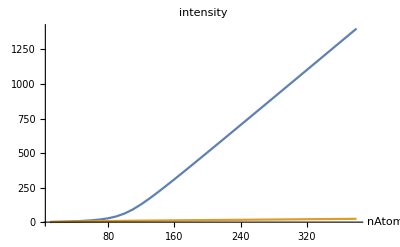

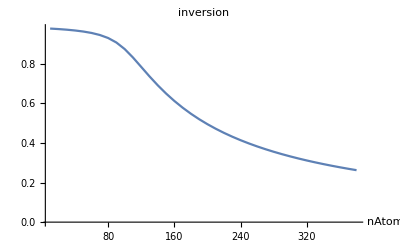

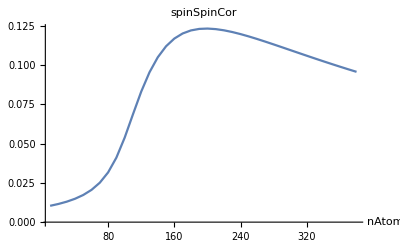

```mathematica
ListLinePlot[{intensityPlot,intensityUnCorPlot},PlotRange->All,PlotLabel->"intensity",AxesLabel->{"nAtom"}]
ListLinePlot[inversionPlot,PlotRange->All,PlotLabel->"inversion",AxesLabel->{"nAtom"}]
ListLinePlot[spinSpinCorPlot,PlotRange->All,PlotLabel->"spinSpinCor",AxesLabel->{"nAtom"}]
```